```mathematica
u[j_,n_]:=u[j,n]=u[j,n-1]+(k Δt)/(Δx)^2(u[j+1,n-1]-2u[j,n-1]+u[j-1,n-1])
```

```mathematica
u[0,n_]:=u1[t]/.t->n Δt
```

```mathematica
M= 10;
```

```mathematica
u[M,n_]:=u2[t]/. t-> n Δt
```

```mathematica
u[j_,0]:=u0[x]/.x->j Δx
```

```mathematica
L=π;k=1/4;Δt=.01;Δx=L/M;
```

```mathematica
u0[x_]=100;
```

```mathematica
u1[t_]=0;
```

```mathematica
u2[t_]=0;
```

```mathematica
table0=Table[{Δx j,u[j,0]},{j,0,M}];
```

```mathematica
TableForm[table0]
```

0 | 0
π/10 | 100
π/5 | 100
(3 π)/10 | 100
(2 π)/5 | 100
π/2 | 100
(3 π)/5 | 100
(7 π)/10 | 100
(4 π)/5 | 100
(9 π)/10 | 100
π | 0

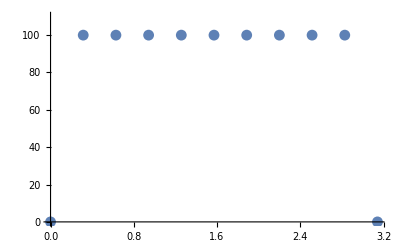

```mathematica
ListPlot[table0, PlotRange->{0,110}]
```